# Mathematica 图形图像语言

## 陆玉柱, 资深软件工程师

# 微信公众号：WolframChina -Graphics- -Graphics-微博公众号：WolframChina -Graphics-

## 概述

本次演讲主要概览简介Mathematica 图形图像语言及相关主要功能，包括：2D/3D primitives, directives, options, 以及软件内置的交换编辑功能比如：drawing palette, Image/Image3D tool bar, context menus。本次演讲还将介绍一些Mathematica的最新支持的图形图像功能比如带照明的立体渲染（Lighted Volume Rendering），非真实感绘制（Non-Photorealistic shading）及客户自定义图形显示。

## Mathematica 图形图像（Graphics）语言简介

Mathematica 图形图像（Graphics）语言是所有图形图像函数的基础, 所有图形图像函数都是通过Graphics语言来显示，交互，输出，打印...

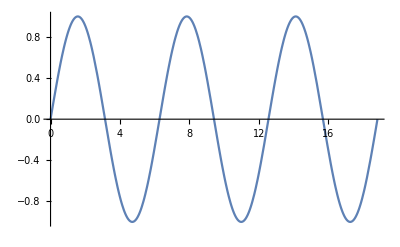

```mathematica
p=Plot[Sin[x],{x,0,6Pi}]
```

```mathematica
p//InputForm
```

### Graphics语言的构成: 元素（Primitives）/指令（Directives）/选项（Options）

#### 元素（Primitives）: Point/Line/Polygon/Sphere/Raster3D.... 指令（Directives）: Texture, RGBColor, FaceForm, EdgeForm, Thickness, Dashing... 选项（Options）: ImageSize, ViewPoint, AspectRatios.....

#### 二维：Graphics

```mathematica
Graphics[{FaceForm[Blue],EdgeForm[{Red,Thick,Dashed}],Polygon[{{0,0},{1,0},{0.5,1}},VertexColors->{Red, Green}],Disk[{2,2},.5]},Axes->True,PlotLabel->三角形与圆]
```

#### 三维：Graphics3D

```mathematica
Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-1.99},{2,2,-1}]},Axes->True]
```

## 图形图像的交互

### 右键菜单

```mathematica
Graphics[{FaceForm[Blue],EdgeForm[{Red,Thick,Dashed}],Polygon[{{0,0},{1,0},{0.5,1}},VertexColors->{Red, Green}],Disk[{2,2},.5]},Axes->True,PlotLabel->三角形与圆]
```

```mathematica
Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-1.99},{2,2,-1}]},Axes->True]
```

#### 工具栏

选择Image/Image3D后弹出工具栏

```mathematica
Image[-Graphics-]
```

```mathematica
Import["ExampleData/CTengine.tiff","Image3D"]
```

#### 鼠标交互

双击二维元素编辑

```mathematica
Graphics[{FaceForm[Blue],EdgeForm[{Red,Thick,Dashed}],Polygon[{{0,0},{1,0},{0.5,1}},VertexColors->{Red, Green}],Disk[{2,2},.5]},Axes->True,PlotLabel->三角形与圆]
```

旋转/移动/放大 三维物体

```mathematica
Graphics3D[Sphere[]]
```

## 自定义鼠标交互

用户可在程序中添加自定义的鼠标/键盘交互

#### Mouseover

```mathematica
Graphics[Mouseover[{Red,Disk[]},{Blue,Disk[]}],ImageSize->150]
```

-Graphics-

```mathematica
Graphics3D[Mouseover[{Red,Sphere[]},{Blue,Sphere[]}],ImageSize->150]
```

-Graphics3D-

#### Tooltip

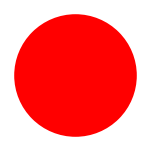

```mathematica
Graphics[Tooltip[{Red,Disk[]},"这是个红色的圆"],ImageSize->150]
```

```mathematica
Graphics3D[Tooltip[{Red,Sphere[]},"球"],ImageSize->150]
```

-Graphics3D-

#### StatusArea/Annotation/MousePosition/Locator/ClickPane...

```mathematica
createCircle[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=With[{a=Det[({{x1, y1, 1}, {x2, y2, 1}, {x3, y3, 1}})],d=-Det[({{x1^2+y1^2, y1, 1}, {x2^2+y2^2, y2, 1}, {x3^2+y3^2, y3, 1}})],e=Det[({{x1^2+y1^2, x1, 1}, {x2^2+y2^2, x2, 1}, {x3^2+y3^2, x3, 1}})],f=-Det[({{x1^2+y1^2, x1, y1}, {x2^2+y2^2, x2, y2}, {x3^2+y3^2, x3, y3}})]},Circle[{-d/(2 a),-e/(2 a)},√((d^2+e^2)/(4 a^2)-f/a)]];
```

```mathematica
createCircle[pts_]:={};
DynamicModule[{pts={},c={}},ClickPane[Framed@Graphics[{Dynamic[c],Point[Dynamic[pts]]},PlotRange->5],(If[Length[pts]<3,AppendTo[pts,#],pts={#}];c=createCircle[pts])&]]
```

#### EventHandler

```mathematica
DynamicModule[{col=Green},EventHandler[Dynamic[Graphics[{col,Disk[]},ImageSize->Tiny]],{"MouseClicked":>(col=col/.{Red->Green,Green->Blue,Blue->Red})}]]
```

```mathematica
DynamicModule[{col=Green},EventHandler[Dynamic[Graphics[{col,Disk[]},ImageSize->Tiny]],{"MouseDown":>(col=col/.{Red->Green,Green->Red}),
"MouseUp":>(col=col/.{Red->Green,Green->Red})}]]
```

#### Dynamic and Manipulate

```mathematica
Framed@DynamicModule[{contents={}},EventHandler[Graphics[{PointSize[0.1],Point[Dynamic[contents=Map[If[#[[1,2]]≥0,{#[[1]]-#[[2]],#[[2]]+{0,0.001}},{{#[[1,1]],0},{1,-0.8}#[[2]]}]&,contents];Map[First,contents]]]},PlotRange->{{0,1},{0,1}}],"MouseDown":>(AppendTo[contents,{MousePosition["Graphics"],{0,0}}])]]
```

```mathematica
Manipulate[Graphics[{color,Disk[{0,0},r]},PlotRange->1],{color,Purple},{{r,0.5},0,1}]
```

## 绘画工具

Graphics/Drawing Tools

## 图形图像选项

Format/Option Inspector/Graphics Options

## 带照明的立体渲染（Lighted Volume Rendering）

```mathematica
Graphics3D[{Specularity[White,30],Raster3D[RawArray["Byte",Import["ExampleData/CThead.tiff","Data"]],{{-1,-1,-1},{1,1,1}},{0,255},ColorFunction->#,Method->{ "VolumeLighting"->"EnhancedEdge","InterpolateValues"->True}]},ViewPoint->{-3.2,0.89,-0.34},ImageSize->300,Lighting->{{"Directional",White,ImageScaled[{0,0,2}]}}]&/@{(Blend[{{1,RGBColor[1.,1.,1.,0]},{0,RGBColor[0.,0.,0.,0.]},{0.35,RGBColor[0.33,0.33,0.33,0]},{0.66,RGBColor[0.66,0.66,0.66,0]},{0.21,RGBColor[0.19,0.19,0.19,0.34]},{0.19,RGBColor[0.17,0.17,0.17,0]},{0.27,RGBColor[0.25,0.25,0.25,0]}},#]&),(Blend[{{0, RGBColor[0.035,0.058,0,0]},{0.1, RGBColor[0.015,0,0.035,0]},{0.2, RGBColor[0,0,0,0.032]},{0.3, RGBColor[0.103,0.032,0,0]},{0.4, RGBColor[0,0,0,0]},{0.5, RGBColor[0.202,0.203,0.218,0.337]},{0.6, RGBColor[0.9,0.9,0.9,0.457]},{0.7, RGBColor[0.98,0.97,1,0.682]},{0.8, RGBColor[1,1,1,0.794]},{0.9, RGBColor[0.95,0.97,0.95,0.842]},{1, RGBColor[1,1,1,0.962]}}, #] &),(Blend[{{1,RGBColor[1., 1., 1., 1.]}, {0, RGBColor[0., 0., 0., 0]}, {0.32, RGBColor[0.5, 0.5, 0.5, 0.65]},{0.66,RGBColor[ 0.66, 0.66, 0.66, 0.66]}, {0.07,RGBColor[0.12, 0.12, 0.12, 0]}}, #]& )}
```

## 非真实感绘制（Non-Photorealistic shading）

### New NPO for 3D graphics ToonShading, GoochShading, StippleShading, HalftoneShading, HatchShading

### ToonShading

```mathematica
Graphics3D[{ToonShading[ColorData[35,"ColorList"]],KnotData["SolomonSeal","ImageData"]},Lighting->#,ImageSize->300]&/@{"Accent",{{"Directional",White,{{1,-1,2},{0,0,0}}}}}
```

### GoochShading

```mathematica
Graphics3D[{GoochShading[ColorData[35,"ColorList"]],KnotData["SolomonSeal","ImageData"]},Lighting->#,ImageSize->300]&/@{"Accent",{{"Directional",White,{{1,-1,2},{0,0,0}}}}}
```

{-Graphics3D-,-Graphics3D-}

### StippleShading

```mathematica
Manipulate[Graphics3D[{StippleShading[d],ExampleData[{"Geometry3D","Cow"},"GraphicsComplex"]},Lighting->#,ImageSize->300]&/@{"Accent",{{"Directional",White,{{1,-1,2},{0,0,0}}}}},{{d,0.5},0,1}]
```

### HatchShading

```mathematica
Graphics3D[{HatchShading[],Sphere[]},Lighting->#,ImageSize->300]&/@{"Accent",{{"Directional",White,{{1,-1,2},{0,0,0}}}}}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
tones=ImageData[#]&/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
cow=ExampleData[{"Geometry3D","Cow"},"GraphicsComplex"]/.Polygon[pts_]:>Polygon[pts,VertexTextureCoordinates->"Box"];
```

```mathematica
Graphics3D[{SurfaceAppearance["RampShading","StepCount"->10,"Tiling"->{2,2},"FeatureColor"->GrayLevel[0],"UseScreenSpace"->0,"IsTwoTone"->1,"LuminanceModifier"->0.5,EdgeForm[],Texture[tones]],cow},Method->{"TextureSampling"->"Nearest"},Lighting->{{"Directional",White,{{1,-1,2},{0,0,0}}}},ImageSize->500,Boxed->False]
```

```mathematica
tones=ImageData[#]&/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
Graphics3D[{SurfaceAppearance["RampShading","StepCount"->10,"Tiling"->{2,2},"FeatureColor"->GrayLevel[0],"UseScreenSpace"->0,"IsTwoTone"->1,"LuminanceModifier"->0.5,EdgeForm[],Texture[tones]],cow},Method->{"TextureSampling"->"Nearest"},Lighting->{{"Directional",White,{{1,-1,2},{0,0,0}}}},ImageSize->500,Boxed->False]
```

### HalftoneShading

```mathematica
Graphics3D[{HalftoneShading[0.5,Black,#],ExampleData[{"Geometry3D","Galleon"},"GraphicsComplex"]},Boxed->False,Method->{"ShrinkWrap" -> True},ImageSize->200,Lighting->{{"Directional",White,{{1,-1,2},{0,0,0}}}}]&/@{"Disk","Hexagon", "Line","Square","Triangle"}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Line pattern and tiling directives for 2D graphics Hatching, Tiling

### HatchFilling

```mathematica
Plot[{Sin[x]+x/2,Sin[x]+x}, {x, 0, 10},Filling->{1->{2}},FillingStyle->HatchFilling[.3]]
```

-Graphics-

### PatternFilling

```mathematica
Plot[{Sin[x]+x/2,Sin[x]+x}, {x, 0, 10},Filling->{1->{2}},FillingStyle->PatternFilling[-Graphics-]]
```

-Graphics-

## 客户自定义图形显示

## Surface Appearance

#### 1. 自定义渲染模式

#### 2. 二维/三维

#### 3. GLSL 1.2 标准

### 非真实感绘制是建立在 SurfaceAppearance之上

```mathematica
Graphics3D[{ToonShading[],Sphere[]},Lighting->"Accent"]
```

### 结构

```mathematica
shader=<|
"Name"->"DepthOfField",
"Attributes"-><|"a_vertex"->"ATTRIB_VERTEX"|>,"Parameters"-><|"Matrix"->{"u_transform","TRANSFORMMATRIX","MATRIX4"},"ColorRamp"->{"u_colorRamp",Automatic,"TEXTURE"},"Size"->{"size",360,"NUMBER"},"FocusDepth"->{"focus",0.5,"NUMBER"},"Maxfilter"->{"maxfilter",20,"NUMBER"}|>,"ShaderPrograms"-><|"GLFragmentProgram"->"uniform sampler2D u_colorRamp; uniform float size; uniform float focus; uniform float maxfilter; varying vec4 v_pos; void main(){ float offset=1.0/size; vec2 texCoord = v_pos.xy/2.0+vec2(.5,0.5); vec3 sum = texture2D(u_colorRamp, texCoord).rgb; float block = max(0, texture2D(u_colorRamp, texCoord).a - focus) * maxfilter; float count = 1.0; for(float i = -block; i < block; i = i+1.0) { { sum = sum + texture2D(u_colorRamp, clamp(texCoord+vec2(offset * i, 0), 0.0, 1.0)).rgb; count = count + 1.0;}} gl_FragColor.rgb = sum/count; gl_FragColor.a = 1.0;}","GLVertexProgram"->"attribute vec4 a_vertex; uniform mat4 u_transform; varying vec4 v_pos; void main(){v_pos = u_transform * a_vertex; gl_Position = u_transform * a_vertex;}"|>
|>;
```

```mathematica
Dataset[shader]
```

### Example 1: Depth of Field

```mathematica
ColorDepth[g_,size_]:=ColorCombine[Append[ColorSeparate[Rasterize@Graphics3D[g,Method->{"OneLayer"->{"Color",1}},Boxed->False,ImageSize->size]],First@ColorSeparate@Rasterize@Graphics3D[g,Method->{"OneLayer"->{"Depth",1}},Boxed->False,ImageSize->size]],"RGB"];
FE`Evaluate@Evaluate[FEPrivate`AddSurfaceAppearanceDefinition@shader];
Graphics3DWithDOF[g_,size_,focus_,maxFilter_]:=
Graphics[{Texture[ColorDepth[g,size]],Directive[SurfaceAppearance["DepthOfField","Size"->size,"FocusDepth"->focus,"Maxfilter"->maxFilter]],Polygon[{{0,0},{1,0},{1,1},{0,1}}]},PlotRange->{{0,1},{0,1}},ImageSize->size];
```

```mathematica
Manipulate[Graphics3DWithDOF[Normal[ExampleData[{"Geometry3D","Galleon"},"GraphicsComplex"]],500,f,m],{{f,0.5},0,1},{{m,10},0,30}]
```

```mathematica
Manipulate[Graphics3DWithDOF[Normal[ExampleData[{"Geometry3D","Beethoven"},"GraphicsComplex"]],500,f,m],{{f,0.5},0,1},{{m,20},5,50}]
```

## 资源链接

[文档中心（Documentation）](https://reference.wolfram.com/language/index.html.zh?source=footer)

[项目演示（Demonstration）](https://demonstrations.wolfram.com)